```mathematica
𝒟=ProbabilityDistribution[Piecewise[{{1/2(2-y), 0<=y<=2}, {0, !(0<=y<=2)}}],{y,-∞,∞}]
```

ProbabilityDistribution[Piecewise[{{(2-x)/2, 0≤x≤2}, {0, True}}],{x,-∞,∞}]

```mathematica
PDF[𝒟,y]
```

Piecewise[{{(2-y)/2, 0≤y≤2}, {0, True}}]

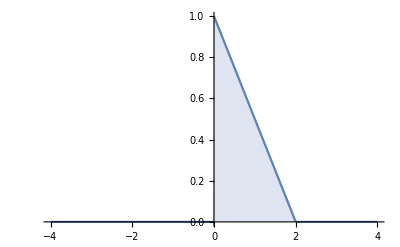

```mathematica
Plot[PDF[𝒟,y],{y,-4,4},Filling->Axis,PlotRange->All]
```

```mathematica
CDF[𝒟,y]
```

Piecewise[{{1, y>2}, {1/4 (4 y-y^2), 0<y≤2}, {0, True}}]

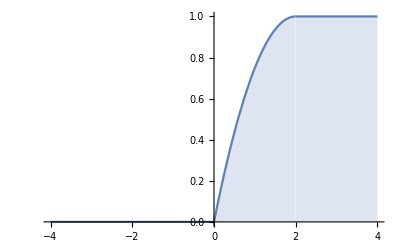

```mathematica
Plot[CDF[𝒟,y],{y,-4,4},Filling->Axis,PlotRange->All]
```

```mathematica
Mean[𝒟]
```

2/3

```mathematica
Variance[𝒟]
```

2/9

```mathematica
MomentGeneratingFunction[𝒟,t]
```

(-1+ⅇ^(2 t)-2 t)/(2 t^2)

```mathematica
FactorialMomentGeneratingFunction[𝒟,t]
```

(-1+t^2-2 Log[t])/(2 Log[t]^2)

```mathematica
Kurtosis[𝒟]
```

12/5

```mathematica
TrimmedMean[𝒟]
```

1/135 (270+√5-19 √95)

```mathematica
TrimmedVariance[𝒟]
```

(2 (215+19 √19))/3645

```mathematica
RandomReal[2,2]
```

{0.287977,0.849202}

```mathematica
Last@Convergents[#]&/@RandomReal[2,2]
```

{1838056/51048863,2505452/7897945}

```mathematica
Probability[x>1838056/51048863,x\[Distributed]𝒟]
```

2513000357127225/2605986413592769

```mathematica
Probability[x<2505452/7897945,x\[Distributed]𝒟]
```

18218599665064/62377535223025

```mathematica
Probability[1838056/51048863<x<2505452/7897945,x\[Distributed]𝒟]
```

41677182189412893483024371616/162555009304607543935942306225

```mathematica
NProbability[1838056/51048863<x<2505452/7897945,x\[Distributed]𝒟,WorkingPrecision->100]
```

0.2563881751027132062769507725466234209061360557240344500408653717814246756018549693876136664209231258

```mathematica
Last@Convergents[#]&/@RandomReal[2,4]
```

{33239201/19587213,11340315/6015313,11800595/17097193,344125/225282}

```mathematica
Sort[Last@Convergents[#]&/@RandomReal[2,4]]
```

{268184/856727,44820533/43617959,21294599/18471521,9737630/6513093}

```mathematica
Probability[x>44820533/43617959\[Conditioned]x>=268184/856727,x\[Distributed]𝒟]
```

99847237621569427739929/300492042070146995761924

```mathematica
Probability[x>44820533/43617959\[Conditioned]268184/856727<=x<=21294599/18471521,x\[Distributed]𝒟]
```

22809825420900084508344865335933470184/212974889340085559357686664678220789059

```mathematica
Probability[44820533/43617959<=x<=21294599/18471521\[Conditioned]268184/856727<=x<=9737630/6513093,x\[Distributed]𝒟]
```

2177103311595069148974830656499896298927915341200186/24747623268244617334794096549837275384717339142442061

```mathematica
ResourceFunction["RandomPolynomial"][x,4]
```

46+60 x-39 x^2-70 x^3+35 x^4

```mathematica
TransformedDistribution[46+60 x-39 x^2-70 x^3+35 x^4,x\[Distributed]𝒟]
```

TransformedDistribution[46+60 x-39 x^2-70 x^3+35 x^4,x\[Distributed]ProbabilityDistribution[Piecewise[{{(2-x)/2, 0≤x≤2}, {0, True}}],{x,-∞,∞}]]

```mathematica
Mean[TransformedDistribution[46+60 x-39 x^2-70 x^3+35 x^4,x\[Distributed]𝒟]]
```

124/3

```mathematica
Variance[TransformedDistribution[46+60 x-39 x^2-70 x^3+35 x^4,x\[Distributed]𝒟]]
```

23548/45

```mathematica
MomentGeneratingFunction[TransformedDistribution[46+60 x,x\[Distributed]𝒟],t]
```

(ⅇ^(46 t) (-1+ⅇ^(120 t)-120 t))/(7200 t^2)

```mathematica
MomentGeneratingFunction[TransformedDistribution[46+60 x-39 x^2,x\[Distributed]𝒟],t]
```

1/(2028 t)ⅇ^(10 t) (13-13 ⅇ^(36 t)+16 ⅇ^(768 t/13) √(39 π) √t Erf[10 √(3/13) √t]+16 ⅇ^(768 t/13) √(39 π) √t Erf[16 √(3/13) √t])

```mathematica
Cumulant[𝒟,5]
```

-32/567